```mathematica
ClearAll[u1,u2]
```

```mathematica
{u1'[t] == u1[t] u2[t],
u2'[t] == (1/2) (u2[t]^2 - κ^2 u1[t]^2)}
```

{u1'[t]==u1[t] u2[t],u2'[t]==1/2 (-κ^2 u1[t]^2+u2[t]^2)}

```mathematica
usols=(DSolve[{u1'[t]==u1[t] u2[t],u2'[t]==1/2 (u2[t]^2-κ^2 u1[t]^2)},{u1[t],u2[t]},{t}]//Simplify)/.{C[1]-> c1,C[2]-> c2}
```

{{u2[t]→-2 √((c1^4 (-c2+t)^2)/((c1^2 (-c2+t)^2+4 κ^2)^2)),u1[t]→(4 c1)/(c1^2 (-c2+t)^2+4 κ^2)},{u2[t]→2 √((c1^4 (c2+t)^2)/((c1^2 (c2+t)^2+4 κ^2)^2)),u1[t]→(4 c1)/(c1^2 (c2+t)^2+4 κ^2)}}

```mathematica
t1sols=Solve[vx== (u1[t]/.usols[[1]]),t]//Simplify
t2sols=Solve[vx== (u1[t]/.usols[[2]]),t]//Simplify
```

{{t→c2-(2 √(c1^2 vx (c1-vx κ^2)))/(c1^2 vx)},{t→c2+(2 √(c1^2 vx (c1-vx κ^2)))/(c1^2 vx)}}

{{t→-c2-(2 √(c1^2 vx (c1-vx κ^2)))/(c1^2 vx)},{t→-c2+(2 √(c1^2 vx (c1-vx κ^2)))/(c1^2 vx)}}

```mathematica
(u2[t]/.usols[[1]])/.t1sols//Simplify
(u2[t]/.usols[[2]])/.t2sols//Simplify
```

{-√(vx (c1-vx κ^2)),-√(vx (c1-vx κ^2))}

{√(vx (c1-vx κ^2)),√(vx (c1-vx κ^2))}

```mathematica
4
```

```mathematica
c2
```

c2

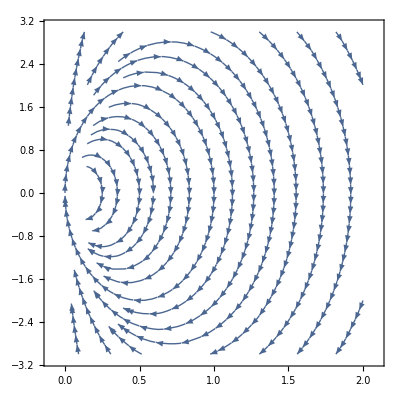

```mathematica
StreamPlot[{u1 u2,(1/2) (u2^2 - κ^2 u1^2)}/.κ-> 4,{u1,0,2},{u2,-3,3}]
```

```mathematica
Integrate[((4 c1)/(c1^2 (c2+t)^2+4 κ^2)/.c2-> -1/2),t]
```

```mathematica
(((2 ArcTan[(c1 (-1/2+t))/(2 κ)])/κ)/.t-> 1/2)-(((2 ArcTan[(c1 (-1/2+t))/(2 κ)])/κ)/.t-> 0)
```

```mathematica
Solve[(2 ArcTan[c1/(4 κ)])/κ==1/2,c1]
```

{{c1→ConditionalExpression[4 κ Tan[κ/4],(-2 π≤Re[κ]<2 π&&Im[κ]<0)||-2 π<Re[κ]<2 π||(-2 π<Re[κ]≤2 π&&Im[κ]>0)]}}

```mathematica
(Integrate[(4 c1)/(c1^2 (-c2+t)^2+4 κ^2)/.c2-> 1/2 ,t]/.t-> 1)-(Integrate[(4 c1)/(c1^2 (-c2+t)^2+4 κ^2)/.c2-> 1/2,t]/.t-> 1/2)
```

(2 ArcTan[c1/(4 κ)])/κ

```mathematica
(Integrate[4 c1/(4κ^2+c1^2(t+c2)^2),t]/.t-> 1/2)-(Integrate[4 c1/(4κ^2+c1^2(t+c2)^2),t]/.t-> 0)
```

-(2 ArcTan[(c1 c2)/(2 κ)])/κ+(2 ArcTan[(c1 (1/2+c2))/(2 κ)])/κ

```mathematica
-(2 ArcTan[(c1 c2)/(2 κ)])/κ+(2 ArcTan[(c1 (1/2+c2))/(2 κ)])/κ==xf/2
```

-(2 ArcTan[(c1 c2)/(2 κ)])/κ+(2 ArcTan[(c1 (1/2+c2))/(2 κ)])/κ==xf/2

```mathematica
Solve[-(4 Log[c1^2 c2+4 κ^2])/c1+(4 Log[c1^2 (1/2+c2)+4 κ^2])/c1==1/2,c2]
```

```mathematica
{{c2->(c1^2+8 κ^2-8 ⅇ^(c1/8) κ^2)/(2 c1^2 (-1+ⅇ^(c1/8)))}}//Simplify
```

{{c2→1/(2 (-1+ⅇ^(c1/8)))-(4 κ^2)/c1^2}}

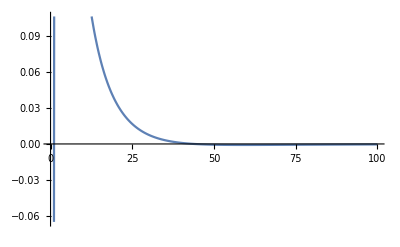

```mathematica
Plot[1/(2 (-1+ⅇ^(c1/8)))-(4 κ^2)/c1^2/.κ-> 1,{c1,0,100}]
```

```mathematica
1/(2 (-1+ⅇ^((c1 xf)/8)))-(4 κ^2)/c1^2== -1/2
```

1/(2 (-1+ⅇ^((c1 xf)/8)))-(4 κ^2)/c1^2==-1/2

```mathematica
Solve[1/(2 (-1+ⅇ^(c1/8)))-(4 κ^2)/c1^2==-1/2,c1]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[1/(2 (-1+ⅇ^(c1/8)))-(4 κ^2)/c1^2==-1/2,c1]

```mathematica
Manipulate[Plot[{Sqrt[vx(c1-vx)],Sqrt[vx(c1-vx)]},{vx,0,1}],{c1,-1,2}]
```

```mathematica
((1/2+τ)-c2)^2 == ((1/2-τ)+c2)^2
```

(1/2-c2+τ)^2==(1/2+c2-τ)^2

```mathematica
SolveAlways[(1/2-c2+τ)^2==(1/2+c2-τ)^2,c2]
```

{}

```mathematica
Solve[(3/4-c2)^2==(1/4+c2)^2,{c2}]
```

{{c2→1/4}}

```mathematica
1/(t-1/2)^2
```

1/(-1/2+t)^2

```mathematica
Manipulate[Plot[{1/(t+c)^2,-1/(t-c)^2},{t,0,1}],{c,-1,1}]
```

```mathematica
u1=4 c1/(4κ^2+c1^2(t+c2)^2)/.c2-> -1/2
```

(4 c1)/(c1^2 (-1/2+t)^2+4 κ^2)

```mathematica
u2= 2 √((C[1]^4 (t+C[2])^2)/((4 κ^2+C[1]^2 (t+C[2])^2)^2))/.{C[1]-> c1,C[2]-> -1/2}
```

2 √((c1^4 (-1/2+t)^2)/((c1^2 (-1/2+t)^2+4 κ^2)^2))

```mathematica
Manipulate[Plot[{2 √((c1^4 (-1/2+t)^2)/((c1^2 (-1/2+t)^2+4 κ^2)^2)),-2 √((c1^4 (+1/2+t)^2)/((c1^2 (+1/2+t)^2+4 κ^2)^2))},{t,0,1}],{c1,1,8},{κ,1,10}]
```

```mathematica
u1
```

(4 c1)/(c1^2 (-1/2+t)^2+4 κ^2)

```mathematica
-(2 ArcTan[(c1 c2)/(2 κ)])/κ+(2 ArcTan[(c1 (1/2+c2))/(2 κ)])/κ==1/2
```

```mathematica
Tan[-(2 ArcTan[(c1 c2)/(2 κ)])/κ+(2 ArcTan[(c1 (1/2+c2))/(2 κ)])/κ]==Tan[1/2]
```

```mathematica
-Tan[(2 ArcTan[(c1 c2)/(2 κ)])/κ-(2 ArcTan[(c1 (1/2+c2))/(2 κ)])/κ]==Tan[1/2]//TrigExpand
```

```mathematica
-((2 Cos[ArcTan[(c1 c2)/(2 κ)]/κ] Cos[ArcTan[(c1 (1/2+c2))/(2 κ)]/κ]^2 Sin[ArcTan[(c1 c2)/(2 κ)]/κ])/(Cos[ArcTan[(c1 c2)/(2 κ)]/κ]^2 Cos[ArcTan[(c1 (1/2+c2))/(2 κ)]/κ]^2-Cos[ArcTan[(c1 (1/2+c2))/(2 κ)]/κ]^2 Sin[ArcTan[(c1 c2)/(2 κ)]/κ]^2+4 Cos[ArcTan[(c1 c2)/(2 κ)]/κ] Cos[ArcTan[(c1 (1/2+c2))/(2 κ)]/κ] Sin[ArcTan[(c1 c2)/(2 κ)]/κ] Sin[ArcTan[(c1 (1/2+c2))/(2 κ)]/κ]-Cos[ArcTan[(c1 c2)/(2 κ)]/κ]^2 Sin[ArcTan[(c1 (1/2+c2))/(2 κ)]/κ]^2+Sin[ArcTan[(c1 c2)/(2 κ)]/κ]^2 Sin[ArcTan[(c1 (1/2+c2))/(2 κ)]/κ]^2))+(2 Cos[ArcTan[(c1 c2)/(2 κ)]/κ]^2 Cos[ArcTan[(c1 (1/2+c2))/(2 κ)]/κ] Sin[ArcTan[(c1 (1/2+c2))/(2 κ)]/κ])/(Cos[ArcTan[(c1 c2)/(2 κ)]/κ]^2 Cos[ArcTan[(c1 (1/2+c2))/(2 κ)]/κ]^2-Cos[ArcTan[(c1 (1/2+c2))/(2 κ)]/κ]^2 Sin[ArcTan[(c1 c2)/(2 κ)]/κ]^2+4 Cos[ArcTan[(c1 c2)/(2 κ)]/κ] Cos[ArcTan[(c1 (1/2+c2))/(2 κ)]/κ] Sin[ArcTan[(c1 c2)/(2 κ)]/κ] Sin[ArcTan[(c1 (1/2+c2))/(2 κ)]/κ]-Cos[ArcTan[(c1 c2)/(2 κ)]/κ]^2 Sin[ArcTan[(c1 (1/2+c2))/(2 κ)]/κ]^2+Sin[ArcTan[(c1 c2)/(2 κ)]/κ]^2 Sin[ArcTan[(c1 (1/2+c2))/(2 κ)]/κ]^2)-(2 Cos[ArcTan[(c1 (1/2+c2))/(2 κ)]/κ] Sin[ArcTan[(c1 c2)/(2 κ)]/κ]^2 Sin[ArcTan[(c1 (1/2+c2))/(2 κ)]/κ])/(Cos[ArcTan[(c1 c2)/(2 κ)]/κ]^2 Cos[ArcTan[(c1 (1/2+c2))/(2 κ)]/κ]^2-Cos[ArcTan[(c1 (1/2+c2))/(2 κ)]/κ]^2 Sin[ArcTan[(c1 c2)/(2 κ)]/κ]^2+4 Cos[ArcTan[(c1 c2)/(2 κ)]/κ] Cos[ArcTan[(c1 (1/2+c2))/(2 κ)]/κ] Sin[ArcTan[(c1 c2)/(2 κ)]/κ] Sin[ArcTan[(c1 (1/2+c2))/(2 κ)]/κ]-Cos[ArcTan[(c1 c2)/(2 κ)]/κ]^2 Sin[ArcTan[(c1 (1/2+c2))/(2 κ)]/κ]^2+Sin[ArcTan[(c1 c2)/(2 κ)]/κ]^2 Sin[ArcTan[(c1 (1/2+c2))/(2 κ)]/κ]^2)+(2 Cos[ArcTan[(c1 c2)/(2 κ)]/κ] Sin[ArcTan[(c1 c2)/(2 κ)]/κ] Sin[ArcTan[(c1 (1/2+c2))/(2 κ)]/κ]^2)/(Cos[ArcTan[(c1 c2)/(2 κ)]/κ]^2 Cos[ArcTan[(c1 (1/2+c2))/(2 κ)]/κ]^2-Cos[ArcTan[(c1 (1/2+c2))/(2 κ)]/κ]^2 Sin[ArcTan[(c1 c2)/(2 κ)]/κ]^2+4 Cos[ArcTan[(c1 c2)/(2 κ)]/κ] Cos[ArcTan[(c1 (1/2+c2))/(2 κ)]/κ] Sin[ArcTan[(c1 c2)/(2 κ)]/κ] Sin[ArcTan[(c1 (1/2+c2))/(2 κ)]/κ]-Cos[ArcTan[(c1 c2)/(2 κ)]/κ]^2 Sin[ArcTan[(c1 (1/2+c2))/(2 κ)]/κ]^2+Sin[ArcTan[(c1 c2)/(2 κ)]/κ]^2 Sin[ArcTan[(c1 (1/2+c2))/(2 κ)]/κ]^2)==Tan[1/2]//Simplify
```

Tan[1/2]+Tan[(2 (ArcTan[(c1 c2)/(2 κ)]-ArcTan[(c1+2 c1 c2)/(4 κ)]))/κ]==0

```mathematica
Tan[1/2]//N
```

0.546302

```mathematica
Tan[(ArcTan[(c1 c2)/(2 κ)]-ArcTan[(c1+2 c1 c2)/(4 κ)])/1]//TrigReduce
```

Tan[ArcTan[(c1 c2)/(2 κ)]-ArcTan[(c1+2 c1 c2)/(4 κ)]]

```mathematica
TrigToExp[Tan[ArcTan[(c1 c2)/(2 κ)]-ArcTan[(c1+2 c1 c2)/(4 κ)]]]
```

```mathematica
(ⅈ (-ⅇ^(1/2 (-Log[1-(ⅈ c1 c2)/(2 κ)]+Log[1+(ⅈ c1 c2)/(2 κ)])+1/2 (Log[1-(ⅈ (c1+2 c1 c2))/(4 κ)]-Log[1+(ⅈ (c1+2 c1 c2))/(4 κ)]))+ⅇ^(1/2 (Log[1-(ⅈ c1 c2)/(2 κ)]-Log[1+(ⅈ c1 c2)/(2 κ)])+1/2 (-Log[1-(ⅈ (c1+2 c1 c2))/(4 κ)]+Log[1+(ⅈ (c1+2 c1 c2))/(4 κ)]))))/(ⅇ^(1/2 (-Log[1-(ⅈ c1 c2)/(2 κ)]+Log[1+(ⅈ c1 c2)/(2 κ)])+1/2 (Log[1-(ⅈ (c1+2 c1 c2))/(4 κ)]-Log[1+(ⅈ (c1+2 c1 c2))/(4 κ)]))+ⅇ^(1/2 (Log[1-(ⅈ c1 c2)/(2 κ)]-Log[1+(ⅈ c1 c2)/(2 κ)])+1/2 (-Log[1-(ⅈ (c1+2 c1 c2))/(4 κ)]+Log[1+(ⅈ (c1+2 c1 c2))/(4 κ)])))//Simplify
```

-(2 c1 κ)/(c1^2 c2 (1+2 c2)+8 κ^2)

```mathematica
-ArcTan[(c1 c2)/(2 κ)]/1+(1 ArcTan[(c1 (1/2+c2))/(2 κ)])/1==κ/4
```

-ArcTan[(c1 c2)/(2 κ)]+ArcTan[(c1 (1/2+c2))/(2 κ)]==κ/4

```mathematica
Tan[-ArcTan[(c1 c2)/(2 κ)]+ArcTan[(c1 (1/2+c2))/(2 κ)]]//TrigToExp//Simplify
```

```mathematica
(2 c1 κ)/(c1^2 c2 (1+2 c2)+8 κ^2)== Tan[κ/4]
```

(2 c1 κ)/(c1^2 c2 (1+2 c2)+8 κ^2)==Tan[κ/4]

```mathematica
2 √((C[1]^4 (t+C[2])^2)/((4 κ^2+C[1]^2 (t+C[2])^2)^2))/.{C[1]-> c1,C[2]->c2}
```

```mathematica
2 √((c1^4 (c2+t)^2)/((c1^2 (c2+t)^2+4 κ^2)^2))/.t-> ts
```

```mathematica
2 √((c1^4 (c2+ts)^2)/((c1^2 (c2+ts)^2+4 κ^2)^2))==0
```

2 √((c1^4 (c2+ts)^2)/((c1^2 (c2+ts)^2+4 κ^2)^2))==0

```mathematica
usols={{u2[t]->-2 √((C[1]^4 (t-C[2])^2)/((4 κ^2+C[1]^2 (t-C[2])^2)^2)),u1[t]->(4 C[1])/(4 κ^2+C[1]^2 (t-C[2])^2)},{u2[t]->2 √((C[1]^4 (t+C[2])^2)/((4 κ^2+C[1]^2 (t+C[2])^2)^2)),u1[t]->(4 C[1])/(4 κ^2+C[1]^2 (t+C[2])^2)}}
```

{{(2 √((c1^4 (-1/2+t)^2)/((c1^2 (-1/2+t)^2+4 κ^2)^2)))[t]→-2 √((C[1]^4 (t-C[2])^2)/((4 κ^2+C[1]^2 (t-C[2])^2)^2)),(4 c1)/(c1^2 (-1/2+t)^2+4 κ^2)[t]→(4 C[1])/(4 κ^2+C[1]^2 (t-C[2])^2)},{(2 √((c1^4 (-1/2+t)^2)/((c1^2 (-1/2+t)^2+4 κ^2)^2)))[t]→2 √((C[1]^4 (t+C[2])^2)/((4 κ^2+C[1]^2 (t+C[2])^2)^2)),(4 c1)/(c1^2 (-1/2+t)^2+4 κ^2)[t]→(4 C[1])/(4 κ^2+C[1]^2 (t+C[2])^2)}}

```mathematica
vx==(u1[t]/.usols)
```

vx=={(4 C[1])/(4 κ^2+C[1]^2 (t-C[2])^2),(4 C[1])/(4 κ^2+C[1]^2 (t+C[2])^2)}

```mathematica
usols
```

{{(2 √((c1^4 (-1/2+t)^2)/((c1^2 (-1/2+t)^2+4 κ^2)^2)))[t]→-2 √((C[1]^4 (t-C[2])^2)/((4 κ^2+C[1]^2 (t-C[2])^2)^2)),(4 c1)/(c1^2 (-1/2+t)^2+4 κ^2)[t]→(4 C[1])/(4 κ^2+C[1]^2 (t-C[2])^2)},{(2 √((c1^4 (-1/2+t)^2)/((c1^2 (-1/2+t)^2+4 κ^2)^2)))[t]→2 √((C[1]^4 (t+C[2])^2)/((4 κ^2+C[1]^2 (t+C[2])^2)^2)),(4 c1)/(c1^2 (-1/2+t)^2+4 κ^2)[t]→(4 C[1])/(4 κ^2+C[1]^2 (t+C[2])^2)}}

```mathematica
(*FINAL SOLUTION*)
(*First Half*)
u11Result = (u1[t]/.usols[[2]])/.{c2-> -1/2, c1-> 4 κ Abs[Tan[κ/4]]}//Simplify
u21Result = (u2[t]/.usols[[2]])/.{c2-> -1/2, c1-> 4 κ Abs[Tan[κ/4]]}//Simplify
(*Second Half*)
u12Result = (u1[t]/.usols[[1]])/.{c2-> 1/2, c1-> 4 κ Abs[Tan[κ/4]]}//Simplify
u22Result = (u2[t]/.usols[[1]])/.{c2-> 1/2, c1-> 4 κ Abs[Tan[κ/4]]}//Simplify
```

(4 Abs[Tan[κ/4]])/(κ (1+(1-2 t)^2 Abs[Tan[κ/4]]^2))

4 Abs[Tan[κ/4]]^2 √((1-2 t)^2/((1+(1-2 t)^2 Abs[Tan[κ/4]]^2)^2))

(4 Abs[Tan[κ/4]])/(κ (1+(1-2 t)^2 Abs[Tan[κ/4]]^2))

-4 Abs[Tan[κ/4]]^2 √((1-2 t)^2/((1+(1-2 t)^2 Abs[Tan[κ/4]]^2)^2))

```mathematica
(*BUT NOTICE THEY ARE THE SAME*)
u1Result = (4 Abs[Tan[κ/4]])/(κ (1+(1-2 t)^2 Tan[κ/4]^2))
u2Result = (4 (1-2 t) Tan[κ/4]^2)/(1+(1-2 t)^2 Tan[κ/4]^2)
```

(4 Abs[Tan[κ/4]])/(κ (1+(1-2 t)^2 Tan[κ/4]^2))

(4 (1-2 t) Tan[κ/4]^2)/(1+(1-2 t)^2 Tan[κ/4]^2)

```mathematica
Tan[κ/4]
```

Tan[κ/4]

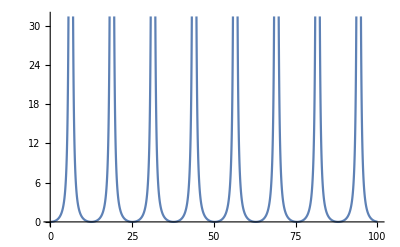

```mathematica
Plot[Tan[κ/4]^2,{κ,0.1,100}]
```

```mathematica
{4 √(((1-2 t)^2 Tan[κ/4]^4)/((1+(1-2 t)^2 Tan[κ/4]^2)^2)),-4 √(((1-2 t)^2 Tan[κ/4]^4)/((1+(1-2 t)^2 Tan[κ/4]^2)^2)),(4 (1-2 t) Tan[κ/4]^2)/(1+(1-2 t)^2 Tan[κ/4]^2)}/.κ-> 1
```

{4 Tan[1/4]^2 √((1-2 t)^2/((1+(1-2 t)^2 Tan[1/4]^2)^2)),-4 Tan[1/4]^2 √((1-2 t)^2/((1+(1-2 t)^2 Tan[1/4]^2)^2)),(4 (1-2 t) Tan[1/4]^2)/(1+(1-2 t)^2 Tan[1/4]^2)}

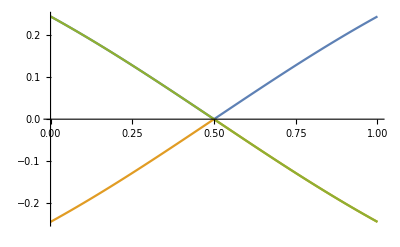

```mathematica
Plot[{4 Tan[1/4]^2 √((1-2 t)^2/((1+(1-2 t)^2 Tan[1/4]^2)^2)),-4 Tan[1/4]^2 √((1-2 t)^2/((1+(1-2 t)^2 Tan[1/4]^2)^2)),(4 (1-2 t) Tan[1/4]^2)/(1+(1-2 t)^2 Tan[1/4]^2)},{t,0,1}]
```

```mathematica
4 ((1-2 t) Tan[κ/4]^2)/(1+(1-2 t)^2 Tan[κ/4]^2)
```

(4 (1-2 t) Tan[κ/4]^2)/(1+(1-2 t)^2 Tan[κ/4]^2)

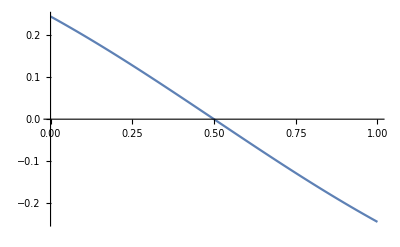

```mathematica
Plot[(4 (1-2 t) Tan[κ/4]^2)/(1+(1-2 t)^2 Tan[κ/4]^2)/.κ-> 1,{t,0,1}]
```

```mathematica
(Integrate[u1Result,t])-(Integrate[u1Result,t]/.t-> 0)//FullSimplify
```

(2 (ArcTan[Tan[κ/4]]+ArcTan[(-1+2 t) Tan[κ/4]]))/(κ Sign[Tan[κ/4]])

```mathematica
Manipulate[Plot[(2 (ArcTan[Tan[κ/4]]+ArcTan[(-1+2 t) Tan[κ/4]]))/(κ Sign[Tan[κ/4]]),{t,0,1}],{κ,0,100}]
```

```mathematica
Manipulate[Plot[u1Result,{t,0,1}],{κ,0,1000}]
```

```mathematica
(2 (ArcTan[Tan[κ/4]]+ArcTan[(-1+2 t) Tan[κ/4]]))/κ/.κ-> 348//N
```

0.00574713 (-0.964594-ArcTan[1.44242 (-1.+2. t)])

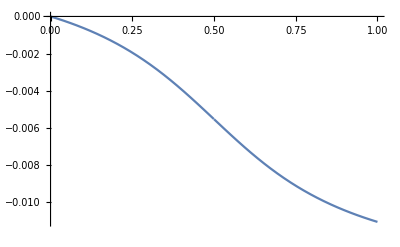

```mathematica
Plot[0.005747126436781609 (-0.9645943005142072-ArcTan[1.4424174716642324 (-1.+2. t)]),{t,0,1}]
```

```mathematica
u1Result
```

```mathematica
Integrate[(4 Tan[κ/4])/(κ (1+(1-2 t)^2 Tan[κ/4]^2)),{t,0,1}]
```

```mathematica
Assuming[κ>0,ConditionalExpression[(4 ArcTan[Tan[κ/4]])/κ,Re[Cot[κ/4]]≠0||Im[Cot[κ/4]]>1||Im[Cot[κ/4]]<-1]]
```

ConditionalExpression[(4 ArcTan[Tan[κ/4]])/κ,Re[Cot[κ/4]]≠0||Im[Cot[κ/4]]>1||Im[Cot[κ/4]]<-1]

```mathematica
Integrate[(4 (1-2 t) Tan[κ/4]^2)/(1+(1-2 t)^2 Tan[κ/4]^2),{t,0,1}]
```

ConditionalExpression[0,Re[Cot[κ/4]]≠0||Im[Cot[κ/4]]>1||Im[Cot[κ/4]]<-1]

```mathematica
Cot[κ/4] == 0
```

Cot[κ/4]==0

```mathematica
Solve[Cot[κ/4]==0,{κ}]
```

{{κ→ConditionalExpression[4 (π/2+π C[1]),C[1]∈Integers]}}

```mathematica
ComplexExpand[Im[Cot[κ/4]]]
```

0

```mathematica
TrigToExp[Cot[κ/4]]
```

-(ⅈ (ⅇ^(-(ⅈ κ)/4)+ⅇ^((ⅈ κ)/4)))/(ⅇ^(-(ⅈ κ)/4)-ⅇ^((ⅈ κ)/4))

```mathematica
Simplify[-(ⅈ (ⅇ^(-(ⅈ κ)/4)+ⅇ^((ⅈ κ)/4)))/(ⅇ^(-(ⅈ κ)/4)-ⅇ^((ⅈ κ)/4))]
```

(ⅈ (1+ⅇ^((ⅈ κ)/2)))/(-1+ⅇ^((ⅈ κ)/2))

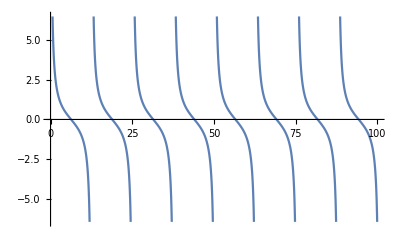

```mathematica
Plot[Cot[κ/4],{κ,0,100}]
```

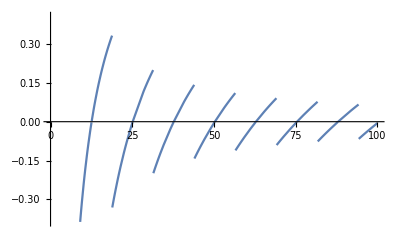

```mathematica
Plot[(4 ArcTan[Tan[κ/4]])/κ,{κ,0,100},WorkingPrecision->MachinePrecision]
```

```mathematica
(4 ArcTan[Tan[κ/4]])/κ== 1
```

(4 ArcTan[Tan[κ/4]])/κ==1

```mathematica
xResult = Integrate[u1Result,t]-(Integrate[u1Result,t]/.t-> 0)//Simplify
```

(2 (ArcTan[Tan[κ/4]]-ArcTan[(1-2 t) Tan[κ/4]]))/κ

```mathematica
hResult = Integrate[u2Result,t] - ( Integrate[u2Result,t]/.t-> 0)//Simplify
```

```mathematica
Log[Sec[κ/4]^2]-Log[1+(1-2 t)^2 Tan[κ/4]^2]//FullSimplify
```

```mathematica
Log[Sec[κ/4]^2]-Log[1+(1-2 t)^2 Tan[κ/4]^2]/.κ-> 1
```

2 Log[Sec[1/4]]-Log[1+(1-2 t)^2 Tan[1/4]^2]

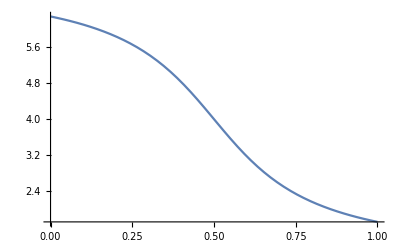

```mathematica
Plot[(2 (κ/4-ArcTan[(1-2 t) Tan[κ/4]]))/1/.κ-> 8,{t,0,1}]
```

```mathematica
Manipulate[Plot[hResult,{t,0,1}],{κ,1,100}]
```

```mathematica
Tan[2]
```

Tan[2]

```mathematica
ArcTan[N[Tan[2]]]
```

-1.14159

```mathematica
ArcTan[(1-2 t) Tan[κ/4]]
```

ArcTan[(1-2 t) Tan[κ/4]]

```mathematica
Manipulate[Plot[ArcTan[(1-2 t) Tan[κ/4]],{t,0,1}],{κ,-10.,10.}]
```

```mathematica
u2Result
```

(4 (1-2 t) Tan[κ/4]^2)/(1+(1-2 t)^2 Tan[κ/4]^2)

```mathematica
Sqrt[(u2Result)^2]
```

4 √(((1-2 t)^2 Tan[κ/4]^4)/((1+(1-2 t)^2 Tan[κ/4]^2)^2))

```mathematica
Manipulate[Plot[{4 √(((1-2 t)^2 Tan[κ/4]^4)/((1+(1-2 t)^2 Tan[κ/4]^2)^2)),-4 √(((1-2 t)^2 Tan[κ/4]^4)/((1+(1-2 t)^2 Tan[κ/4]^2)^2)),(4 (1-2 t) Tan[κ/4]^2)/(1+(1-2 t)^2 Tan[κ/4]^2)},{t,0,1}],{κ,0,100}]
```

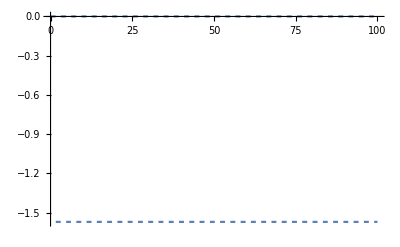

```mathematica
Plot[ArcTan[Tan[x]]-Mod[x,π/2],{x,0,100}]
```

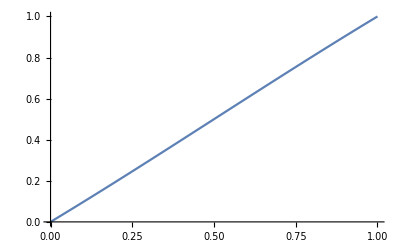

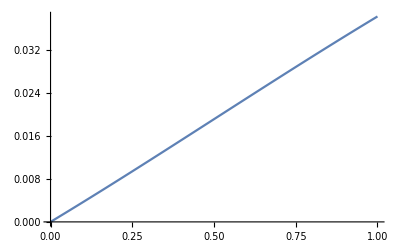

```mathematica
Plot[xResult/.κ-> 1,{t,0,1}]
Plot[xResult/.κ-> 1+8π,{t,0,1}]
```

```mathematica
u1Result*xf/tf/.κ-> xf*β/.β-> 1
u2Result*κ/(β tf)/.{β-> 1,κ-> xf}
```

(4 Tan[xf/4])/(tf (1+(1-2 t)^2 Tan[xf/4]^2))

(4 (1-2 t) xf Tan[xf/4]^2)/(tf (1+(1-2 t)^2 Tan[xf/4]^2))

```mathematica
Manipulate[Plot[{(4 Tan[xf/4])/(tf (1+(1-2 t)^2 Tan[xf/4]^2)),(4 (1-2 t) xf Tan[xf/4]^2)/(tf (1+(1-2 t)^2 Tan[xf/4]^2))},{t,0,tf}],{tf,1,10},{xf,1,1+8π}]
```

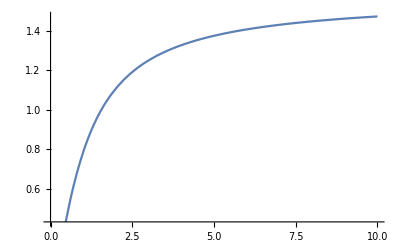

```mathematica
Plot[ArcTan[x],{x,0,10}]
```

```mathematica
Integrate[(4 c1)/(c1^2 (c2+t)^2+4 κ^2)/.c2-> -1/2,{t,0,1/2}]
```

ConditionalExpression[(2 ArcTan[c1/(4 κ)])/κ,Re[κ/c1]≠0||Im[κ/c1]>1/4||Im[κ/c1]<-1/4]

```mathematica
(2 ArcTan[c1/(4 κ)])/κ
```

(2 ArcTan[c1/(4 κ)])/κ

```mathematica
Plot3D[(2 ArcTan[c1/(4 κ)])/κ,{c1,-5.,5.},{κ,0.1,10}]
```

-Graphics3D-

```mathematica
u1Result
```

(4 Tan[κ/4])/(κ (1+(1-2 t)^2 Tan[κ/4]^2))

```mathematica
Manipulate[Plot[(4 Tan[κ/4])/(κ (1+(1-2 t)^2 Tan[κ/4]^2)),{t,0,1}],{κ,0,18π}]
```

```mathematica
usols
```

{{u2[t]→-2 √((c1^4 (-c2+t)^2)/((c1^2 (-c2+t)^2+4 κ^2)^2)),u1[t]→(4 c1)/(c1^2 (-c2+t)^2+4 κ^2)},{u2[t]→2 √((c1^4 (c2+t)^2)/((c1^2 (c2+t)^2+4 κ^2)^2)),u1[t]→(4 c1)/(c1^2 (c2+t)^2+4 κ^2)}}

```mathematica
Integrate[(4 c1)/(c1^2 (c2+t)^2+4 κ^2),t]
```

(2 ArcTan[(c1 (c2+t))/(2 κ)])/κ